# Optimización de Redes Bayesianas por Algoritmo Genético

### Autor: Carlos Manuel Rodríguez Martínez E-Mail: fis.carlosmanuel@gmail.com

## Resumen

Implementación de redes bayesianas con optimizador genético. Permite realizar inferencias sobre una red bayesiana, calcular probabilidades de observación de eventos, y optimizar la estructura del modelo a partir de una base de datos.
Este paquete cuenta con varias secciones:

Inferencia - Algoritmos para hacer inferencia y cálculo de probabilidades a partir de una red bayesiana.
Generación de población - Funciones para generar la población inicial que será optimizada por medio de un algoritmo genético.
Métricas y evaluación - Colección de métricas para evaluar la población y funciones relacionadas.
Selección, crossover y mutación - Especificación operaciones del algoritmo genético. Implementa una selección proporcional, crossover aleatorio y mutación aleatoria.
Optimización de estructura - Implementa la interfaz de usuario para automatizar el proceso de optimización.
Reporte de optimización - Funciones para generar reportes del proceso de optiimzación.


Referencias:
1- Levine, Nicholas D., “Using Minimum Description Length for Discretization Classification of Data Modeled by Bayesian Networks” (2011). Applied Mathematics Graduate Theses & Dissertations. 21. 
https://scholar.colorado.edu/appm_gradetds/21
2- Friedman, Goldszmidt, “Learning Bayesian Networks from Data” (1998). Presentation.
3- Eugene Charniak, “Bayesian Networks without Tears”. AI Magazine. Winter 1991.
4- Nicandro Cruz, “Building Bayesian Networks from Data: A Constraint-based Approach”. PhD Thesis. Department of Psychology. The University of Sheffield.

## Inferencia

En el contexto de redes bayesianas la predicción de una variable clase consiste en realizar una inferencia probabilística. Esta se calcula evaluando la probabilidad de observar una instancia y escongiendo la instancia que la maximice.

Por ejemplo, una red bayesiana optimizada para la base de datos Iris al recibir la instancia {2, 0, 1, “?”} calcula la probabilidad de todos los posibles reemplazos de “?”:

P({2, 0, 1, “Iris-setosa”}) = 0.0
P({2, 0, 1, “Iris-virginica”}) = 0.000592593
P({2, 0, 1, “Iris-versicolor”}) = 0.0260741

Dado que la probabilidad se maximiza con la instancia {2, 0, 1, “Iris-versicolor”} se escoge “Iris-versicolor” como la mejor predicción. Para realizar la inferencia se pueden utilizar dos interfaces.
BayesInfer[dag, dataset, query] realiza la inferencia calculando las probabilidades marginales en el momento de evaluar el query. Esto es útil si sólo se desea hacer una evaluación rápida. Cada query debe contener el símbolo “?” sobre la variable que se desee predecir. La estructura de la red dag se define como un grafo donde deben ser especificadas las relaciones entre vértices. E.g.: {1->2, 1->3, 2->3, 3->4}.
BayesInfer[dag, possibleValues, marginals, query] realiza la inferencia a partir de las probabilidades marginales precalculadas en marginals y la lista de posibles valores possibleValues.
Es posible utilizar la misma interfaz con la función BayesProbabilities que calcula las probabilidades asociadas a cada cada posible reemplazo de “?”.
PrintBayesProbabilities[dag, dataset, instance, attributes : None] imprime las probabilidades marginales utilizadas en el proceso de inferencia. Se puede utilizar una lista de nombre de atributos dada en attributes para reemplazar los índices de los vértices por el nombre de los atributos.

### Implementación:

```mathematica
Parents[graph_,node_]:=Cases[graph, p_->node:>p];
PossibleValues[dataset_,attribute_]:=DeleteDuplicates[dataset[[All,attribute]]];
```

```mathematica
CalculateParents[dag_,numOfAttributes_]:=Association@Map[#->Parents[dag,#]&,Range[numOfAttributes]];
CalculatePossibleValues[dataset_]:=Association@Table[attribute->PossibleValues[dataset,attribute],{attribute,1,Length[First[dataset]]}];
```

```mathematica
ParentConfigurations[dataset_,parents_,possibleValues_]:=Tuples[Map[possibleValues[#]&,parents]];
ParentConfigurationsOfNode[dataset_,parents_,possibleValues_,node_]:=ParentConfigurations[dataset,parents[node],possibleValues];
```

Cálculo de posibles configuraciones de nodos y padres.

```mathematica
AttributeConfigurations[parents_,data_,attribute_]:=Map[<|"ParentValues"->#[[parents[attribute]]],"Value"->#[[attribute]]|>&,data];
```

Cálculo de probabilidad condicional P(A| B,C, ...) dado el valor del nodo A y el valor de sus padres B, C, ...

```mathematica
ConditionalProbability[data_,parents_,node_,nodeValue_,parentValues_]:=Block[{attConf,num,den},
attConf = AttributeConfigurations[parents,data,node];
num = Length[Cases[attConf,KeyValuePattern[{"ParentValues"->parentValues, "Value"->nodeValue}]]];
den = Length[Cases[attConf,KeyValuePattern["ParentValues"->parentValues]]];
If[den ≠ 0,num/den,0.0]
];
CalculateMarginals[dataset_,parents_,possibleValues_]:=Association@Flatten@Table[
<|"Node"->i,"Value"->val,"ParentValues"->parentValues|>->N@ConditionalProbability[dataset,parents,i,val,parentValues],
{i,1,Length[First[dataset]]},{val,possibleValues[i]},{parentValues,ParentConfigurationsOfNode[dataset,parents,possibleValues,i]}
];
```

Inferencia a partir de probabilidades marginales precalculadas.

```mathematica
InstanceProbability[parents_,marginals_Association,instance_]:=Block[{key},
Apply[Times,
Table[
key = <|"Node"->i,"Value"->instance[[i]],"ParentValues"->instance[[parents[i]]]|>;
If[KeyExistsQ[marginals,key],
marginals[<|"Node"->i,"Value"->instance[[i]],"ParentValues"->instance[[parents[i]]]|>],
0.0
]
,
{i,1,Length[instance]}]
]
];

BayesProbabilities[parents_,possibleValues_,marginals_,query_]:=Block[{queryPosition,queryInstances,evaluated},
queryPosition = First[FirstPosition[query,"?"]];
If[queryPosition=="NotFound",Return[$Failed]];
queryInstances = Map[ReplaceAll[query,"?"->#]&,possibleValues[queryPosition]];
evaluated = MapThread[{#1,InstanceProbability[parents,marginals,#2]}&,{possibleValues[queryPosition],queryInstances}];

SortBy[evaluated,Last]
];
BayesInfer[parents_,possibleValues_,marginals_,query_]:=Block[{queryPosition,queryInstances,evaluated},
queryPosition = First[FirstPosition[query,"?"]];
If[queryPosition=="NotFound",Return[$Failed]];
queryInstances = Map[ReplaceAll[query,"?"->#]&,possibleValues[queryPosition]];
evaluated = MapThread[{#1,InstanceProbability[parents,marginals,#2]}&,{possibleValues[queryPosition],queryInstances}];

First@First@MaximalBy[evaluated,Last]
];
```

Imprime las probabilidades marginales usadas en el cálculo de la probabilidad de una instancia.

```mathematica
PrintBayesProbabilities[dag_,dataset_,instance_,attributes_ : None]:=Block[{begin,middle,end,attrNames,n= Length[First[dataset]]},
attrNames = If[attributes===None,Range[n],attributes];
Grid[
Table[
begin = {"P(",Subscript["x",attrNames[[i]]],"=",instance[[i]]};
middle = Switch[Length[Parents[dag,i]],
0,{")="},
1,{"| ",Subscript["x",First@attrNames[[Parents[dag,i]]]],"=",First@instance[[Parents[dag,i]]],")="},
_,{"| ",Subscript["x",attrNames[[Parents[dag,i]]]],"=",instance[[Parents[dag,i]]],")="}
];
end = {N@ConditionalProbability[dataset,CalculateParents[dag,Length[First[dataset]]],i,instance[[i]],instance[[Parents[dag,i]]]]};
Join[begin,middle,end],
{i,1,n}
],
Alignment->Left
]
];
```

```mathematica
LoadDataset[path_]:=Block[{attributes,dataset,possibleValues},
{{attributes},dataset} = TakeDrop[Import[path],1];
possibleValues = CalculatePossibleValues[dataset];
<|"Attributes"->attributes,"Dataset"->dataset,"PossibleValues"->possibleValues|>
];
```

### Ejemplo:

```mathematica
irisDataset = LoadDataset[FileNameJoin[{NotebookDirectory[],"Datasets","iris.csv"}]];
```

Cálculo de probabilidades a partir de la base de datos.

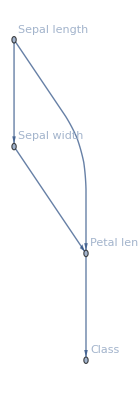

```mathematica
Graph[{1->2,1->3,2->3,3->4},VertexLabels->Thread[Range[Length[irisDataset["Attributes"]]]->irisDataset["Attributes"]]]
```

```mathematica
PrintBayesProbabilities[{1->2,1->3,2->3,3->4},irisDataset["Dataset"],{0,2,0,"Iris-setosa"},irisDataset["Attributes"]]
```

P( | x_(Sepal length) | = | 0 | )= | 0.393333 |  |  |  | 
P( | x_(Sepal width) | = | 2 | |  | x_(Sepal length) | = | 0 | )= | 0.661017
P( | x_(Petal length) | = | 0 | |  | x_{Sepal length,Sepal width} | = | {0,2} | )= | 1.
P( | x_Class | = | Iris-setosa | |  | x_(Petal length) | = | 0 | )= | 1.

Cálculo de probabilidades a partir de tabla de probabilidades marginales.

```mathematica
parents = CalculateParents[{1->2,1->3,2->3,3->4},Length[irisAttributes]]
```

<|1→{},2→{1},3→{1,2},4→{3}|>

```mathematica
marginals = CalculateMarginals[irisDataset["Dataset"],parents,irisDataset["PossibleValues"]]
```

<|<|Node→1,Value→0,ParentValues→{}|>→0.393333,<|Node→1,Value→1,ParentValues→{}|>→0.266667,<|Node→1,Value→2,ParentValues→{}|>→0.34,<|Node→2,Value→2,ParentValues→{0}|>→0.661017,<|Node→2,Value→2,ParentValues→{1}|>→0.15,<|Node→2,Value→2,ParentValues→{2}|>→0.431373,<|Node→2,Value→1,ParentValues→{0}|>→0.118644,<|Node→2,Value→1,ParentValues→{1}|>→0.2,<|Node→2,Value→1,ParentValues→{2}|>→0.215686,<|Node→2,Value→0,ParentValues→{0}|>→0.220339,<|Node→2,Value→0,ParentValues→{1}|>→0.65,<|Node→2,Value→0,ParentValues→{2}|>→0.352941,<|Node→3,Value→0,ParentValues→{0,2}|>→1.,<|Node→3,Value→0,ParentValues→{0,1}|>→0.857143,<|Node→3,Value→0,ParentValues→{0,0}|>→0.153846,<|Node→3,Value→0,ParentValues→{1,2}|>→0.5,<|Node→3,Value→0,ParentValues→{1,1}|>→0.,<|Node→3,Value→0,ParentValues→{1,0}|>→0.,<|Node→3,Value→0,ParentValues→{2,2}|>→0.,<|Node→3,Value→0,ParentValues→{2,1}|>→0.,<|Node→3,Value→0,ParentValues→{2,0}|>→0.,<|Node→3,Value→1,ParentValues→{0,2}|>→0.,<|Node→3,Value→1,ParentValues→{0,1}|>→0.142857,<|Node→3,Value→1,ParentValues→{0,0}|>→0.846154,<|Node→3,Value→1,ParentValues→{1,2}|>→0.166667,<|Node→3,Value→1,ParentValues→{1,1}|>→0.625,<|Node→3,Value→1,ParentValues→{1,0}|>→0.653846,<|Node→3,Value→1,ParentValues→{2,2}|>→0.227273,<|Node→3,Value→1,ParentValues→{2,1}|>→0.0909091,<|Node→3,Value→1,ParentValues→{2,0}|>→0.222222,<|Node→3,Value→2,ParentValues→{0,2}|>→0.,<|Node→3,Value→2,ParentValues→{0,1}|>→0.,<|Node→3,Value→2,ParentValues→{0,0}|>→0.,<|Node→3,Value→2,ParentValues→{1,2}|>→0.333333,<|Node→3,Value→2,ParentValues→{1,1}|>→0.375,<|Node→3,Value→2,ParentValues→{1,0}|>→0.346154,<|Node→3,Value→2,ParentValues→{2,2}|>→0.772727,<|Node→3,Value→2,ParentValues→{2,1}|>→0.909091,<|Node→3,Value→2,ParentValues→{2,0}|>→0.777778,<|Node→4,Value→Iris-setosa,ParentValues→{0}|>→1.,<|Node→4,Value→Iris-setosa,ParentValues→{1}|>→0.,<|Node→4,Value→Iris-setosa,ParentValues→{2}|>→0.,<|Node→4,Value→Iris-versicolor,ParentValues→{0}|>→0.,<|Node→4,Value→Iris-versicolor,ParentValues→{1}|>→0.977778,<|Node→4,Value→Iris-versicolor,ParentValues→{2}|>→0.109091,<|Node→4,Value→Iris-virginica,ParentValues→{0}|>→0.,<|Node→4,Value→Iris-virginica,ParentValues→{1}|>→0.0222222,<|Node→4,Value→Iris-virginica,ParentValues→{2}|>→0.890909|>

```mathematica
marginals[<|"Node"->3,"Value"->1,"ParentValues"->{1,0}|>]
```

0.653846

```mathematica
BayesProbabilities[parents,irisDataset["PossibleValues"],marginals,{0,2,0,"?"}]
```

{{Iris-versicolor,0.},{Iris-virginica,0.},{Iris-setosa,0.26}}

```mathematica
BayesProbabilities[parents,irisDataset["PossibleValues"],marginals,{2,0,1,"?"}]
```

{{Iris-setosa,0.},{Iris-virginica,0.000592593},{Iris-versicolor,0.0260741}}

```mathematica
RepeatedTiming[InstanceProbability[parents,marginals,{0,2,0,"Iris-setosa"}]]
```

{0.000043,0.26}

## Generación de población

El generador de población es un generador de DAGs que selecciona los grafos correspondientes a un DAG por medio de los eigenvalores de su matriz de adyacencia.

GeneratePopulation[n, size] genera un arreglo de una cantidad size de matrices de adyacencia que representan DAGs de orden n.

### Implementación:

```mathematica
CheckComplex[l_]:=Apply[Or,Map[MatchQ[#,_Complex]&,l]];
CheckNegative[l_]:=Apply[Or,Map[Re[#]≤0&,l]];
IsDAG[matrix_]:=Block[{ev},
If[Tr[matrix]≠0,Return[False]];
ev = N[Eigenvalues[matrix+IdentityMatrix[Length[matrix]]]];
If[CheckNegative[ev] || CheckComplex[ev],
Return[False],
Return[True]
];
];
SimplifyToDAG[matrix_]:=Block[{i,positions,output = matrix},
positions = RandomSample[Position[matrix,1]];
output = matrix;
For[i=1,!IsDAG[output],i++,output = ReplacePart[output,positions[[i]]->0]];
Return[output];
];
```

El generador de población crea una semilla aleatoria inicial y simplifica quitando entradas 1 de manera aleatoria hasta que la matriz representa a un DAG.

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"Extra","AdvancedMapping.wl"}]]; (* Permite hacer mapeos con un contador de progreso *)
```

```mathematica
Normal@AdjacencyMatrix@DirectedGraph[RandomGraph[{10,10}],"Acyclic"]
```

{{0,0,1,1,1,0,1,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
GeneratePopulation[n_,size_]:=Table[Normal@AdjacencyMatrix@DirectedGraph[RandomGraph[{n,n}],"Acyclic"],size];
```

### Ejemplo:

Generación de población con 4 atributos y 20 individuos.

```mathematica
Map[MatrixForm,GeneratePopulation[4,20]]
```

{(0 | 1 | 1 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 1 | 1 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 1 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 1 | 0 | 1
0 | 0 | 1 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 1 | 0 | 1
0 | 0 | 1 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 1 | 1 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 1 | 0 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 0 | 1 | 1
0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 0 | 1 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 1 | 1 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 0 | 1 | 1
0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 1 | 0 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 1 | 0 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 1 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 1 | 0 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 0 | 1 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 0)}

## Métrica precisión de clasificación

La métrica de precisión de clasificación mide el porcentaje de instancias correctamente clasificadas.
CorrectlyClassifiedPercentageScore[dag, dataset] calcula el porcentaje de instancias de la base de datos dataset que fueron correctamente clasificadas bajo el modelo dado por dag.
CorrectlyClassifiedPercentageScore[dag, trainingDataset, testDataset] permite separar la base de datos de entranamiento trainingDataset  y la base de datos de prueba testDataset.
CorrectlyClassifiedPercentageScore[dag, trainingDataset, testDataset, classIndex] permite especificar el índice dado por classIndex de la clase a predecir.

### Implementación:

```mathematica
CorrectlyClassifiedPercentage[parents_,marginals_,possibleValues_,testDataset_,classIndex_]:=Block[{testQuery,prediction,testResults},
testQuery = Map[ReplacePart[#,classIndex->"?"]&,testDataset];
prediction = Map[BayesInfer[parents,possibleValues,marginals,#]&,testQuery];
testResults = MapThread[#1==#2&,{testDataset[[All,classIndex]],prediction}];

Count[testResults,True]/Length[testResults]
];
CorrectlyClassifiedPercentageTotal[dag_,possibleValues_,trainingDataset_,testDataset_]:=Block[{parents,marginals,testQuery,prediction,testResults},
parents = CalculateParents[dag,Length[First[trainingDataset]]];
marginals = CalculateMarginals[trainingDataset,parents,possibleValues];
Table[CorrectlyClassifiedPercentage[parents,marginals,possibleValues,testDataset,att],{att,Length[possibleValues]}]
];
```

```mathematica
CorrectlyClassifiedPercentageScore[dag_,possibleValues_,trainingDataset_,testDataset_,classIndex_]:=Block[{parents,marginals,testQuery,prediction,testResults},
parents = CalculateParents[dag,Length[First[trainingDataset]]];
marginals = CalculateMarginals[trainingDataset,parents,possibleValues];
testQuery = Map[ReplacePart[#,classIndex->"?"]&,testDataset];
prediction = Map[BayesInfer[parents,possibleValues,marginals,#]&,testQuery];
testResults = MapThread[#1==#2&,{testDataset[[All,classIndex]],prediction}];

Count[testResults,True]/Length[testResults]
];
CorrectlyClassifiedPercentageScore[dag_,possibleValues_,dataset_]:=CorrectlyClassifiedPercentageScore[dag,possibleValues,dataset,dataset,Length[First[dataset]]];
CorrectlyClassifiedPercentageScore[dag_,possibleValues_,trainingDataset_,testDataset_]:=CorrectlyClassifiedPercentageScore[dag,possibleValues,trainingDataset,testDataset,Length[First[trainingDataset]]];
```

```mathematica
parents = CalculateParents[{1->2,1->3,2->3,2->4,3->4},Length[First[irisDataset["Dataset"]]]]
```

<|1→{},2→{1},3→{1,2},4→{2,3}|>

```mathematica
marginals = CalculateMarginals[irisDataset["Dataset"],parents,irisDataset["PossibleValues"]];
```

```mathematica
testQuery = Map[ReplacePart[#,4->"?"]&,irisDataset["Dataset"]];
```

```mathematica
prediction = Map[BayesInfer[parents,irisDataset["PossibleValues"],marginals,#]&,testQuery];
```

```mathematica
testResults = MapThread[#1==#2&,{irisDataset["Dataset"][[All,4]],prediction}];
```

### Ejemplo:

Para un modelo dado por el siguiente grafo:

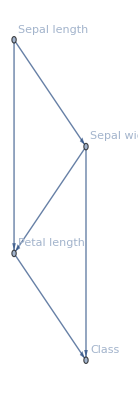

```mathematica
Graph[{1->2,1->3,2->3,2->4,3->4},VertexLabels->Thread[Range[Length[irisDataset["Attributes"]]]->irisDataset["Attributes"]]]
```

El porcentaje de instancias correctamente clasificadas es:

```mathematica
N@CorrectlyClassifiedPercentageScore[{1->2,1->3,2->3,2->4,3->4},irisDataset["PossibleValues"],irisDataset["Dataset"]]
```

0.953333

Al reducir la complejidad del modelo disminuye la precisión de clasificación.

```mathematica
N@CorrectlyClassifiedPercentageScore[{1->2,2->3},irisDataset["PossibleValues"],irisDataset["Dataset"]]
```

0.333333

Es posible separar el conjunto de entrenamiento y el de prueba.

```mathematica
{train,test} = TakeDrop[RandomSample[irisDataset["Dataset"]],100];
N@CorrectlyClassifiedPercentageScore[{1->2,1->3,2->3,2->4,3->4},irisDataset["PossibleValues"],train,test]
```

0.92

## Métrica MDL

La métrica MDL (Minimum Description Length) toma en cuenta la contribución a la longitud de la descripción de tres aspectos del modelo. La contribución de las variables:

||X_i|| representa el número de valores diferentes que puede tomar la variable X. La contribución del DAG:

donde |Π_i| es la cantidad de padres de X_i. La contribución de los parámetros:

||Π_i|| representa el número de configuraciones posibles de los padres de X_i. En total la contribución del modelo a la longitud de descripción es:

Por último es necesario calcular la contribución de los datos dado el modelo. El modelo está implícito en el cálculo debido a que la probabilidad p(u_i) se calcula haciendo uso del DAG.

El MDL es finalmente calculado por medio de la función MDLScore[dag, trainingDataset, testDataset] y MDLScore[dag, dataset].

### Implementación:

ParentConfigurationsOfNode[dag, dataset, node] implementa el cálculo del número posible de configuraciones ||Π_i|| de los padres del nodo X_i dado por node. Length[Parents[dag, node]] implementa el conteo de la cantidad de padres de X_i denotado por |Π_i|, y el número||X_i|| de valores diferentes que puede tomar la variable X se calcula evaluando Length[possibleValues[node]].

```mathematica
VariablesDL[possibleValues_]:=Block[{n = Length[possibleValues]},
Sum[Log[Length[possibleValues[i]]],{i,1,n}]+Log[n]
];

DAGDL[parents_]:=Block[{n = Length[parents]},
If[parents == <||>,Return[0.0]];
Log[n]*Sum[1+Length[parents[i]],{i,1,n}]
];
ParameterDL[parents_,possibleValues_,dataset_]:=Block[{n = Length[First[dataset]],m=Length[dataset]},
1/2 Log[m]*Sum[Length[ParentConfigurationsOfNode[parents,dataset,i]]*(Length[possibleValues[i]]-1),{i,1,n}]
];
ModelDL[parents_,possibleValues_,dataset_]:=VariablesDL[possibleValues] + DAGDL[parents] + ParameterDL[parents,possibleValues,dataset];
DataDL[parents_,marginals_,dataset_]:=Block[{probabilities},
probabilities = Map[InstanceProbability[parents,marginals,#]&,dataset];
(* Se borran las probabilidades 0.0 para evitar logaritmos infinitos que penalizan al modelo por una ausencia de datos de entrenamiento *)
-Total[Map[Log[#]&,DeleteCases[probabilities,0.0]]]
];

MDLScore[dag_,possibleValues_,trainingDataset_,testDataset_]:=Block[{parents,marginals},
parents = CalculateParents[dag,Length[First[trainingDataset]]];
marginals = CalculateMarginals[trainingDataset,parents,possibleValues];
ModelDL[parents,possibleValues,testDataset] + DataDL[parents,marginals,testDataset]
];
MDLScore[dag_,possibleValues_,dataset_]:=MDLScore[dag,possibleValues,dataset,dataset];
```

### Ejemplo

Para un modelo dado por el siguiente grafo:

```mathematica
Graph[{1->2,1->3,2->3,3->4},VertexLabels->Thread[Range[Length[irisDataset["Attributes"]]]->irisDataset["Attributes"]]]
```

-Graphics-

Su puntuación MDL es:

```mathematica
N@MDLScore[{1->2,1->3,2->3,3->4},irisDataset["PossibleValues"],irisDataset["Dataset"]]
```

465.256

Nótese que es una puntuación mejor que la que se obtiene de un grafo vacío.

```mathematica
N@MDLScore[{},irisDataset["PossibleValues"],irisDataset["Dataset"]]
```

718.195

Es posible utilizar conjuntos diferentes de entrenamiento y de prueba.

```mathematica
{train,test} = TakeDrop[RandomSample[irisDataset["Dataset"]],100];
```

```mathematica
N@MDLScore[{1->2,1->3,2->3,3->4},irisDataset["PossibleValues"],train,test]
```

193.102

## Cálculo de rendimiento

Se implementan varias opciones para el cálculo de rendimiento. Las tres funciones principales son:
EvaluateGenome[dataset, population, ScoreFunction] que evalúa la población dada en population con toda la base de datos dataset. La evaluación se realiza con la función ScoreFunction, que puede ser cualquier función con la forma ScoreFunction[dag, dataset].
EvaluateGenomeWithTestData[{trainingDataset, testDataset}, population, ScoreFunction] que evalúa la población con una base de datos de prueba diferente a la de entrenamiento. ScoreFunction puede ser cualquier función con la forma ScoreFunction[dag, trainDataset, testDataset].
EvaluateGenomeWithMinibatch[dataset, population, miniBatchSize, ScoreFunction] que evalúa con un subconjunto de la base de datos original. ScoreFunction puede ser cualquier función con la forma ScoreFunction[dag, dataset].
EvaluateGenomeWithKFolds[dataset, population, folds, ScoreFunction] que realiza validación cruzada con un número fold de pliegues. ScoreFunction puede ser cualquier función con la forma ScoreFunction[dag, dataset].

### Implementación:

```mathematica
EvaluateGenome[dataset_,possibleValues_,population_, ScoreFunction_]:=ProgressParallelMap[
<|
"Genome"->#,
"Score"->N@ScoreFunction[EdgeList[AdjacencyGraph[#]],possibleValues,dataset]
|>&,
population,
Method->"FinestGrained",
"Label"->"Evaluating population"
];
EvaluateGenomeWithTestData[{trainingDataset_,testDataset_},possibleValues_,population_, ScoreFunction_]:=ProgressParallelMap[
<|
"Genome"->#,
"Score"->N@ScoreFunction[EdgeList[AdjacencyGraph[#]],possibleValues,trainingDataset,testDataset]
|>&,
population,
Method->"FinestGrained",
"Label"->"Evaluating population"
];
EvaluateGenomeWithMinibatch[dataset_,possibleValues_,population_,minibatchSize_ ,ScoreFunction_]:=Block[{minibatch=RandomSample[dataset,minibatchSize]},
ProgressParallelMap[
<|
"Genome"->#,
"Score"->N@ScoreFunction[EdgeList[AdjacencyGraph[#]],possibleValues,minibatch]
|>&,
population,
Method->"FinestGrained",
"Label"->"Evaluating population"
]
];

PartitionIn[l_,n_]:=Partition[l,Round[Length[l]/n]]; (* Particiona una lista en n segmentos *)
GetFold[folds_,i_]:={Apply[Join,Delete[folds,i]],Part[folds,i]}; (* Crea par entrenamiento-prueba para validación cruzada *)
EvaluateGenomeWithKFolds[dataset_,possibleValues_,population_,folds_ ,ScoreFunction_]:=Module[{i,dataFolds,foldResults,collapsed},
dataFolds=PartitionIn[dataset,folds];

(* Evalúa cada pliegue *)
foldResults = ProgressTable[
EvaluateGenomeWithTestData[GetFold[dataFolds,i],possibleValues,population,ScoreFunction],
{i,1,Length[dataFolds]},
"Label"->"Evaluating folds"
];

(* Calcula el promedio de los resultados de cada pliegue y los colapsa en una sola población *)
collapsed = Table[
ReplacePart[First[foldResults][[i]],Key["Score"]->Mean[foldResults[[All,i,"Score"]]]],
{i,1,Length[First[foldResults]]}
];

Return[collapsed];
];
```

### Ejemplo:

Evalúa población con métrica MDL.

```mathematica
EvaluateGenome[irisDataset["Dataset"],irisDataset["PossibleValues"],{({{0, 0, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 0}, {0, 1, 1, 0}}),({{0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {1, 0, 1, 0}}),({{0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 0}, {0, 1, 0, 0}}),({{0, 0, 0, 1}, {1, 0, 1, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}})},MDLScore]
```

{<|Genome→{{0,0,0,0},{1,0,0,0},{0,0,0,0},{0,1,1,0}},Score→534.782|>,<|Genome→{{0,1,0,0},{0,0,0,0},{0,0,0,0},{1,0,1,0}},Score→499.29|>,<|Genome→{{0,0,0,0},{0,0,1,0},{0,0,0,0},{0,1,0,0}},Score→655.638|>,<|Genome→{{0,0,0,1},{1,0,1,0},{0,0,0,1},{0,0,0,0}},Score→533.617|>}

Evalúa población con métrica de precisión de clasificación.

```mathematica
EvaluateGenome[irisDataset["Dataset"],irisDataset["PossibleValues"],{({{0, 0, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 0}, {0, 1, 1, 0}}),({{0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {1, 0, 1, 0}}),({{0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 0}, {0, 1, 0, 0}}),({{0, 0, 0, 1}, {1, 0, 1, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}})},CorrectlyClassifiedPercentageScore]
```

{<|Genome→{{0,0,0,0},{1,0,0,0},{0,0,0,0},{0,1,1,0}},Score→0.953333|>,<|Genome→{{0,1,0,0},{0,0,0,0},{0,0,0,0},{1,0,1,0}},Score→0.953333|>,<|Genome→{{0,0,0,0},{0,0,1,0},{0,0,0,0},{0,1,0,0}},Score→0.586667|>,<|Genome→{{0,0,0,1},{1,0,1,0},{0,0,0,1},{0,0,0,0}},Score→0.953333|>}

Evalúa población usando un minibatch de 50 instancias y usando la métrica MDL.

```mathematica
EvaluateGenomeWithMinibatch[irisDataset["Dataset"],irisDataset["PossibleValues"],{({{0, 0, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 0}, {0, 1, 1, 0}}),({{0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {1, 0, 1, 0}}),({{0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 0}, {0, 1, 0, 0}}),({{0, 0, 0, 1}, {1, 0, 1, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}})},50,MDLScore]
```

{<|Genome→{{0,0,0,0},{1,0,0,0},{0,0,0,0},{0,1,1,0}},Score→220.538|>,<|Genome→{{0,1,0,0},{0,0,0,0},{0,0,0,0},{1,0,1,0}},Score→212.024|>,<|Genome→{{0,0,0,0},{0,0,1,0},{0,0,0,0},{0,1,0,0}},Score→258.717|>,<|Genome→{{0,0,0,1},{1,0,1,0},{0,0,0,1},{0,0,0,0}},Score→219.54|>}

Evalúa población usando validación cruzada con 10 pliegues y la métrica MDL.

```mathematica
EvaluateGenomeWithKFolds[irisDataset["Dataset"],irisDataset["PossibleValues"],{({{0, 0, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 0}, {0, 1, 1, 0}}),({{0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {1, 0, 1, 0}}),({{0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 0}, {0, 1, 0, 0}}),({{0, 0, 0, 1}, {1, 0, 1, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}})},10,MDLScore]
```

{<|Genome→{{0,0,0,0},{1,0,0,0},{0,0,0,0},{0,1,1,0}},Score→98.9979|>,<|Genome→{{0,1,0,0},{0,0,0,0},{0,0,0,0},{1,0,1,0}},Score→94.2562|>,<|Genome→{{0,0,0,0},{0,0,1,0},{0,0,0,0},{0,1,0,0}},Score→113.118|>,<|Genome→{{0,0,0,1},{1,0,1,0},{0,0,0,1},{0,0,0,0}},Score→100.225|>}

## Selección

La selección se hace de manera aleatoria y proporcional, dando preferencia a los individuos más aptos. El algoritmo de selección ordena los individuos según su aptitud escoge un índice aleatorio con mayor peso en los individuos más aptos. ProportionateSelection[population, n, selectionCriteria] realiza la selección a partir de la población evaluada population, tomando n individuos con el criterio de selección selectionCriteria que puede tomar los valores “LessIsBetter” o “MoreIsBetter”.

### Implementación:

```mathematica
ProportionateSelectionIndexes[population_,n_]:=RandomSample[Reverse[Range[population]]->Range[population],n];

ProportionateSelection[population_,n_,"LessIsBetter"]:= Part[SortBy[population,Key["Score"]],ProportionateSelectionIndexes[Length[population],n]];
ProportionateSelection[population_,n_,"MoreIsBetter"]:= Part[Reverse[SortBy[population,Key["Score"]]],ProportionateSelectionIndexes[Length[population],n]]
```

### Ejemplo:

Selección de población basada en la métrica MDL la cual penaliza valores altos.

```mathematica
ProportionateSelection[
{
<|"Genome"->{{0,0,0,0},{1,0,0,0},{0,0,0,0},{0,1,1,0}},"Score"->524.7610289505521|>,
<|"Genome"->{{0,1,0,0},{0,0,0,0},{0,0,0,0},{1,0,1,0}},"Score"->489.268798358215|>,
<|"Genome"->{{0,0,0,0},{0,0,1,0},{0,0,0,0},{0,1,0,0}},"Score"->632.7710420740774|>,
<|"Genome"->{{0,0,0,1},{1,0,1,0},{0,0,0,1},{0,0,0,0}},"Score"->553.6591790004508|>
},2,"LessIsBetter"]
```

{<|Genome→{{0,0,0,0},{1,0,0,0},{0,0,0,0},{0,1,1,0}},Score→524.761|>,<|Genome→{{0,1,0,0},{0,0,0,0},{0,0,0,0},{1,0,1,0}},Score→489.269|>}

Selección de población basada en la métrica de porcentaje de instancias correctamente clasificadas, la cual penaliza valores bajos.

```mathematica
ProportionateSelection[
{
<|"Genome"->{{0,0,0,0},{1,0,0,0},{0,0,0,0},{0,1,1,0}},"Score"->0.9533333333333334|>,<|"Genome"->{{0,1,0,0},{0,0,0,0},{0,0,0,0},{1,0,1,0}},"Score"->0.9533333333333334|>,<|"Genome"->{{0,0,0,0},{0,0,1,0},{0,0,0,0},{0,1,0,0}},"Score"->0.5866666666666667|>,<|"Genome"->{{0,0,0,1},{1,0,1,0},{0,0,0,1},{0,0,0,0}},"Score"->0.9533333333333334|>
},2,"MoreIsBetter"]
```

{<|Genome→{{0,0,0,0},{0,0,1,0},{0,0,0,0},{0,1,0,0}},Score→0.586667|>,<|Genome→{{0,1,0,0},{0,0,0,0},{0,0,0,0},{1,0,1,0}},Score→0.953333|>}

## Crossover

La cruza se realiza de manera aleatoria, seleccionando un valor de cualquiera de ambos padres haciendo un muestreo aleatorio. PopulationCrossover[population, childrenPerCouple] realiza la cruza emparejando aleatoriamente pares de individuos dentro de la población produciendo childrenPerCouple hijos por cada par.

### Implementación:

```mathematica
RandomCrossover[parent1_,parent2_]:=Block[{vector1,vector2,transformed},
vector1 =Flatten[parent1];
vector2 =Flatten[parent2];
transformed = Table[If[RandomInteger[]==1,vector1[[i]],vector2[[i]]],{i,1,Length[vector1]}];
SimplifyToDAG[Partition[transformed,Length[parent1]]]
];
```

```mathematica
PopulationCrossover[population_,childrenPerCouple_]:=Block[{couples,newGeneration},
couples = Partition[RandomSample[population],2];
newGeneration = Flatten[
Map[
Table[RandomCrossover[First[#],Last[#]],childrenPerCouple]&,
couples
],1];
Return[newGeneration];
];
```

### Ejemplo:

Cruza entre los individuos (0 | 0 | 0 | 1
1 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0) y(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 1 | 1 | 0) creando una descendencia de 5 individuos.

```mathematica
Map[MatrixForm,PopulationCrossover[{({{0, 0, 0, 1}, {1, 0, 1, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}}),({{0, 0, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 0}, {0, 1, 1, 0}})},5]]
```

{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0),(0 | 0 | 0 | 1
1 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
1 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
1 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

## Mutación

La mutación se realiza cambiando un solo elemento del genoma en una posición aleatoria. PopulationMutate[population,probability] aplica mutationes aleatoriamente con una probabilidad probability sobre cada individuo de la población. Sólo un alelo es modificado por cada mutación.

### Implementación:

```mathematica
Flip[0]=1;
Flip[1] = 0;
AddOrRemoveVertex[matrix_]:=MapAt[Flip,matrix, RandomInteger[{1,Length[matrix]},2]];
ChangeDirection[matrix_]:=Block[{pos = RandomChoice[Position[matrix,1]]},
ReplacePart[matrix,{pos->Extract[matrix,Reverse[pos]],Reverse[pos]->Extract[matrix,pos]}]
];

Mutate[matrix_]:=If[MemberQ[matrix,1,2],
RandomChoice[{2/3,1/3}->{AddOrRemoveVertex[matrix],ChangeDirection[matrix]}],
AddOrRemoveVertex[matrix]
];
RandomMutate[matrix_,probability_]:=If[RandomReal[]<probability,
Return[SimplifyToDAG[Mutate[matrix]]];
,
Return[matrix]
];
PopulationMutate[population_,probability_]:=Map[RandomMutate[#,probability]&,population];
```

### Ejemplo:

Aplica mutación con 80% de probabilidad.

```mathematica
Map[MatrixForm,PopulationMutate[{({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}}),({{0, 0, 0, 1}, {1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}),({{0, 0, 0, 1}, {1, 0, 1, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}),({{0, 0, 0, 1}, {1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}}),({{0, 0, 0, 1}, {1, 0, 1, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}})},0.8]]
```

{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 1 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 1 | 1
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0),(0 | 0 | 0 | 1
1 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0)}

## Optimización de estructura

GenerateInitialPopulation[size, dataset, opts] genera una población inicial de una cantidad size de individuos y evalúa su rendimiento en la base de datos dataset. Sus posibles argumentos opcionales son:
“ScoringFunction” que puede tomar los valores “MDL” para evaluar usando la métrica MDL y “CorrectlyClassified” para evaluar usando la métrica de porcentaje de instancias correctamente evaluadas.
“TestMethod” puede tomar los valores “UseTrainingSet” para evaluar usando el mismo conjunto de datos de entrenamiento, “UseMiniBatch” para evaluar por medio de minibatches de tamaño especificado en la opción “MiniBatchSize”, y “KFoldCrossValidation” para evaluar usando validación cruzada de n pligues especificados en la opción “Folds”.
“MiniBatchSize” es el tamaño del minibatch. Por defecto no está especificado, por lo que es necesario introducir esta opción explicitamente si se especifica “TestMethod”->”UseMiniBatch”.
“Folds” es el número de pliegues en la validación cruzada. Por defecto tiene el valor de 10.

Generation[dataset, population, survivors, mutationProb, opts] realiza una generación del algoritmo genético con la población population, el número de sobrevivientes survivors, y la probabilidad de mutación mutationProb. Sus posibles argumentos opcionales son:
“ScoringFunction”, “TestMethod”, “MiniBatchSize” y “Folds” usados en la función GenerateInitialPopulation,
“ScoreType” que especifica la preferencia del algoritmo de selección proporcional, y puede tomar los valores “LessIsBetter” para dar preferencia a puntuaciones con menor valor y “MoreIsBetter” para dar preferencia a puntuaciones con mayor valor.

GeneticOptimize[dataset, population, survivors, mutationProb, generations, opts] realiza una cantidad generations de iteraciones del algoritmo evolutivo.

Funciones auxiliares para visualización de resultados:
SelectBest[population, n, scoreType] selecciona los n individuos más aptos de la población de acuerdo al criterio scoreType.
PlotBayesNet[net, attributes] grafica la red bayesiana.
PlotGeneration[generation, attributes, index] grafica los individuos de una generación en la iteración especificada en index.
PopulationCorrectlyClassifiedPercentage[population, testData] calcula el porcentaje de aciertos promedio de una población sobre una base de datos de prueba.

### Implementación:

```mathematica
SelectBest[population_, n_, "LessIsBetter"]:=MinimalBy[population,Key["Score"],n];
SelectBest[population_, n_, "MoreIsBetter"]:=MaximalBy[population,Key["Score"],n];

Options[GenerateInitialPopulation]={"ScoringFunction"->"MDL","TestMethod"->"UseTrainingSet","MiniBatchSize"->None,"Folds"->10};
GenerateInitialPopulation[size_,dataset_ ,possibleValues_,OptionsPattern[]]:=Block[{population,minibatchSize,ScoringFunction,folds},
If[OptionValue["TestMethod"]=="UseMiniBatch",
minibatchSize = If[
(OptionValue["MiniBatchSize"]===None) || (OptionValue["MiniBatchSize"]>Length[dataset]),
Length[dataset],
OptionValue["MiniBatchSize"]
];
];

ScoringFunction = Switch[OptionValue["ScoringFunction"],
"MDL",MDLScore,
"CorrectlyClassified",CorrectlyClassifiedPercentageScore,
_,EmptyScoreFunction
];
folds = If[OptionValue["Folds"]>1,OptionValue["Folds"],2];

population = GeneratePopulation[Length[First[dataset]],size];
Switch[OptionValue["TestMethod"],
"UseTrainingSet",EvaluateGenome[dataset,possibleValues,population,ScoringFunction],
"UseMiniBatch",EvaluateGenomeWithMinibatch[dataset,possibleValues,population,minibatchSize,ScoringFunction],
"KFoldCrossValidation",EvaluateGenomeWithKFolds[dataset,possibleValues,population,folds,ScoringFunction]
]
];

Options[Generation]={"ScoringFunction"->"MDL","ScoreType"->"LessIsBetter","TestMethod"->"UseTrainingSet","MiniBatchSize"->None,"Folds"->10};

Generation[dataset_,possibleValues_,population_,survivors_,mutationProb_,OptionsPattern[]]:=
Block[{minibatchSize,populationSize,childrenPerCouple,fittest,newGeneration,mutated,ScoringFunction,folds},
If[OptionValue["TestMethod"]=="UseMiniBatch",
minibatchSize = If[
OptionValue["MiniBatchSize"]===None || OptionValue["MiniBatchSize"]>Length[dataset],
Length[dataset],
OptionValue["MiniBatchSize"]
];
];

(* Cálculo de parámetros *)
populationSize = Length[population];
childrenPerCouple = (2 populationSize)/survivors;
ScoringFunction = Switch[OptionValue["ScoringFunction"],
"MDL",MDLScore,
"CorrectlyClassified",CorrectlyClassifiedPercentageScore,
_,EmptyScoreFunction
];
folds = If[OptionValue["Folds"]>1,OptionValue["Folds"],2];

(* Selección, cruza y mutación de la población *)
fittest = ProportionateSelection[population,survivors,OptionValue["ScoreType"]];
newGeneration = PopulationCrossover[fittest[[All,"Genome"]],childrenPerCouple];
mutated = PopulationMutate[newGeneration,mutationProb];

(* Evaluación del genoma *)
Switch[OptionValue["TestMethod"],
"UseTrainingSet",EvaluateGenome[dataset,possibleValues,mutated,ScoringFunction],
"UseMiniBatch",EvaluateGenomeWithMinibatch[dataset,possibleValues,mutated,minibatchSize,ScoringFunction],
"KFoldCrossValidation",EvaluateGenomeWithKFolds[dataset,possibleValues,mutated,folds,ScoringFunction]
]
];
GeneticOptimize[dataset_,possibleValues_,population_,survivors_,mutationProb_,generations_,opts:OptionsPattern[]]:=
ProgressNestList[
Generation[dataset,possibleValues,#,survivors,mutationProb,FilterRules[{opts}, Options[Generation]]]&,
population,generations,
"Label"->"Generation"
];
```

```mathematica
PlotBayesNet[net_,attributes_]:=AdjacencyGraph[
net["Genome"],
PlotLabel->net["Score"],
PlotTheme->"ClassicDiagram",
VertexLabels->MapIndexed[First[#2]->#1&,attributes],
VertexSize->Medium,
ImageSize->{400,400},
PlotRangePadding->Scaled[0.2],
Frame->True
];
PlotGeneration[generation_,attributes_,index_]:=Labeled[Map[PlotBayesNet[#,attributes]&,generation],"Generation "<>ToString[index],Top];
PopulationCorrectlyClassifiedPercentage[population_,trainData_,testData_,possibleValues_]:=Block[{populationEvaluation},
populationEvaluation = Map[
CorrectlyClassifiedPercentageTotal[EdgeList@AdjacencyGraph@#,possibleValues,trainData,testData]&,
population
];
Map[Mean,Transpose[populationEvaluation]]
];
```

### Ejemplo

Se usa la base de datos Iris.

```mathematica
dataset = LoadDataset[FileNameJoin[{NotebookDirectory[],"Datasets","bmv.csv"}]];
```

Primero se genera una población de 50 individuos:

```mathematica
population = GenerateInitialPopulation[50,dataset["Dataset"],dataset["PossibleValues"],"TestMethod"->"UseMiniBatch","MiniBatchSize"->2500];
```

Se optimiza por medio de un algoritmo genético con 10 supervividentes por generación, 50% de probabilidad de mutación y 20 generaciones:

```mathematica
result = ProgressGeneticOptimize[dataset["Attributes"],dataset["Dataset"],dataset["PossibleValues"],population,20,0.3,30,"TestMethod"->"UseMiniBatch","MiniBatchSize"->2500];
```

Los individuos más aptos por generación son seleccionados y graficados:

```mathematica
fittestByGeneration = Map[SelectBest[#,3,"LessIsBetter"]&,result];
```

```mathematica
generationPlots = MapIndexed[PlotGeneration[#1,dataset["Attributes"],First[#2]]&,fittestByGeneration];
```

Comparación entre primera y última generación:

```mathematica
First@generationPlots
```

{-Graphics-,-Graphics-,-Graphics-}Generation 1

```mathematica
Last@generationPlots
```

{-Graphics-,-Graphics-,-Graphics-}Generation 31

Gráfica de la evolución de la puntuación MDL con respecto a la generación. Nótese la disminución progresiva.

```mathematica
scoreVsK = Table[{k,Mean[result[[k]][[All,"Score"]]]},{k,1,Length[result]}];
```

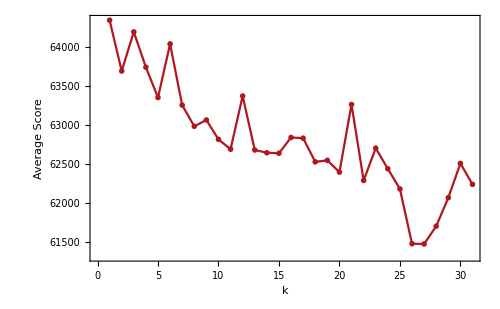

```mathematica
ListLinePlot[
scoreVsK,
PlotTheme->"Monochrome",
FrameLabel->{Style["k",15], Style["Average Score",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->{{},{0}},
Joined->{True,False},
PlotStyle->RGBColor[0.689993, 0.089999, 0.119999],
Frame->True,
ImageSize->500
]
```

Gráfica de la evolución del número de instancias clasificadas correctamente. Nótese el aumento progresivo hasta el valor 1.0.

```mathematica
correctlyClassifiedByGen = ProgressParallelMap[
PopulationCorrectlyClassifiedPercentage[#,RandomSample[dataset["Dataset"],2500],RandomSample[dataset["Dataset"],200],dataset["PossibleValues"]]&,
fittestByGeneration[[All,All,"Genome"]]
];
```

```mathematica
correctlyClassifiedVsK = Map[Thread[{Range[Length[correctlyClassifiedByGen]],#}]&,Transpose@correctlyClassifiedByGen];
```

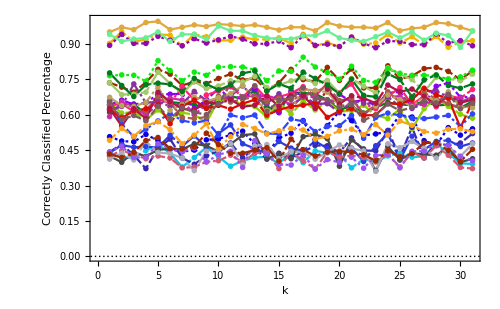

```mathematica
ListLinePlot[
correctlyClassifiedVsK,
PlotTheme->"Monochrome",
FrameLabel->{Style["k",15], Style["Correctly Classified Percentage",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->{{},{0}},
PlotStyle->{RGBColor[0., 0.48, 0.11],RGBColor[0.62, 0.16, 0.],RGBColor[0.05, 0., 0.9],RGBColor[0.54, 0., 0.9400000000000001],RGBColor[0.55, 0.8200000000000001, 0.],RGBColor[0.9400000000000001, 0.7000000000000001, 0.],RGBColor[0.05, 0.78, 0.9],RGBColor[1., 0.14, 0.45],RGBColor[0.8846373407536847, 0.6588036903498808, 0.23569144934791297],RGBColor[0.23169709923722492, 0.15817082448960118, 0.7074650021772924],RGBColor[0.5745444912987769, 0.03639760541796133, 0.66386881591716],RGBColor[0.18919344193752896, 0.2711114902991165, 0.9979054591296619],RGBColor[0.7838449790802127, 0.17111062834517266, 0.6700646752049875],RGBColor[0.5331495135159363, 0.20027294307713261, 0.6145982603673426],RGBColor[0.6296265889868999, 0.7940602411986468, 0.4095657873864673],RGBColor[0.1786819618038562, 0.23733166970840958, 0.8794014903283436],RGBColor[0.2880802611587405, 0.2858036607925627, 0.28012198077361905],RGBColor[0.6394028881427696, 0.3685960874930354, 0.28235132762227555],RGBColor[0.05518431356757714, 0.9237680662787009, 0.05903165255178977],RGBColor[0.8263293896366546, 0.34756579667270526, 0.4464755245089602],RGBColor[0.6760367917306123, 0.6743518300432136, 0.7439753061832197],RGBColor[0.7307519025019802, 0.639283522796873, 0.374405384630381],RGBColor[0.862400498228101, 0.03852773571683965, 0.01142799592840249],RGBColor[0.6877045159466233, 0.08365041695632613, 0.26506242174471906],RGBColor[0.3996581820518086, 0.9365354374698904, 0.5749492621173891],RGBColor[0.491693632658476, 0.34952817057691865, 0.38446934016983514],RGBColor[0.6040551418230642, 0.3278025844022645, 0.9532863396934148],RGBColor[0.9834526153033936, 0.6370698398533381, 0.11400366691822716]},
Frame->True,
ImageSize->500,
PlotRange->{Automatic,{0,1}},
PlotLegends->dataset["Attributes"]
]
```

```mathematica
SaveKernelState[path_:FileNameJoin[{NotebookDirectory[],StringJoin[FileBaseName[NotebookFileName[]],"_state.mx"]}]]:=DumpSave[path,"Global`"];
LoadKernelState[path_:FileNameJoin[{NotebookDirectory[],StringJoin[FileBaseName[NotebookFileName[]],"_state.mx"]}]]:=Get[path];
```

```mathematica
SaveKernelState[]
```

{Global`}

### Optimización interactiva

```mathematica
GetSeconds[time_] := IntegerString[Round[Mod[time, 60]], 10, 2];
GetMinutes[time_]:= IntegerString[Mod[Floor[time/60], 60], 10, 2];
GetHours[time_] := IntegerString[Floor[time/3600], 10, 2];
ClockFormat[time_] := StringJoin[GetHours[time], ":", GetMinutes[time], ":", GetSeconds[time]];

GeneticOptimizeIndicator[indexProgress_,totalSize_,startTime_,fittestIndPlot_,scorePlot_]:=Block[{progressString,remainingTime,remainingTimeString,indicator,ellapsedTimeString},
progressString = Row[{Style["Progress: ",Bold],ToString[indexProgress],"/",ToString[totalSize]}];
ellapsedTimeString = Row[{Style["Ellapsed time: ",Bold],ClockFormat[AbsoluteTime[]-startTime]}];

If[indexProgress ≠ 0,
remainingTime = (AbsoluteTime[]-startTime)/indexProgress(totalSize-indexProgress);
remainingTimeString = Row[{Style["Remaining: ",Bold],ClockFormat[remainingTime]}];
,
remainingTimeString = Row[{Style["Remaining: ", Bold],"Unknown"}];
];

indicator = Panel[
Column[
{
Style["Generation",Bold],
ProgressIndicator[indexProgress,{1,totalSize}],
progressString,
ellapsedTimeString,
remainingTimeString,
Style["Fittest individual: ", Bold],
Row[{fittestIndPlot,scorePlot}]
}
]
];

Return[indicator];
];
ProgressGeneticOptimize[attributes_,dataset_,possibleValues_,population_,survivors_,mutationProb_,generations_,opts:OptionsPattern[]]:=Block[{scorePlot,fittestInd,fittestIndPlot,currentGeneration = population,startTime = AbsoluteTime[],indexProgress = 0,scoreVsK={},allGenerations={population}},
Monitor[
Do[
AppendTo[scoreVsK,Mean[currentGeneration[[All,"Score"]]]];
scorePlot = ListLinePlot[
scoreVsK,
PlotTheme->"Monochrome",
FrameLabel->{Style["Generation",15], Style["Average Score",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->{{},{0}},
Joined->{True,False},
PlotStyle->RGBColor[0.689993, 0.089999, 0.119999],
PlotLabel->"Score",
Frame->True,
ImageSize->500,
PlotRange->All
];
fittestInd = First@SelectBest[currentGeneration,1,"LessIsBetter"];
fittestIndPlot = PlotBayesNet[fittestInd,attributes];

currentGeneration = Generation[dataset,possibleValues,currentGeneration,survivors,mutationProb,FilterRules[{opts}, Options[Generation]]];
AppendTo[allGenerations,currentGeneration];
indexProgress++;
,generations
],
GeneticOptimizeIndicator[indexProgress,generations,startTime,fittestIndPlot,scorePlot]
];

Return[allGenerations];
]
```

```mathematica
testDataset = LoadDataset[FileNameJoin[{NotebookDirectory[],"Datasets","iris.csv"}]];
population = GenerateInitialPopulation[50,testDataset["Dataset"],testDataset["PossibleValues"]];
```

```mathematica
result = ProgressGeneticOptimize[testDataset["Attributes"],testDataset["Dataset"],testDataset["PossibleValues"],population,10,0.3,20];
```

## Reporte de optimización

BayesGeneticTrainAndPlot[datasetPath, populationSize, survivors, mutationProb, generations, opts] genera una lista de gráficas que reportan el progreso de optimización del algoritmo. Acepta las mismas opciones que la función Generation.
BayesGeneticTrainAndExportPlots[datasetPath, populationSize, survivors, mutationProb, generations, opts] genera la lista de gráficas y las exporta a un directorio con el mismo nombre que la base de datos.

### Implementación:

```mathematica
ExportImages[file_,frames_]:=Block[{indexLength,directory,name},
indexLength = Length[IntegerDigits[Length[frames]]];
directory = DirectoryName[file];
name = FileBaseName[file];

MapIndexed[
Export[
FileNameJoin[{directory,StringJoin[name,IntegerString[#2,10,indexLength],".png"]}],
#1
]&,
frames
]
];

Options[BayesGeneticTrainAndPlot]={"ScoringFunction"->"MDL","ScoreType"->"LessIsBetter","TestMethod"->"UseTrainingSet","MiniBatchSize"->None,"Folds"->10};
BayesGeneticTrainAndPlot[attributes_,dataset_,possibleValues_,populationSize_,survivors_,mutationProb_,generations_,opts:OptionsPattern[]]:=Block[{population,iterations,fittestByGeneration,generationPlots,scoreVsK,scoreVsKPlot,correctlyClassifiedByGen,correctlyClassifiedVsK,correctlyClassifiedVsKPlot},

population = GenerateInitialPopulation[populationSize,dataset,possibleValues,FilterRules[{opts}, Options[GenerateInitialPopulation]]];
iterations = ProgressGeneticOptimize[attributes,dataset,possibleValues,population,survivors,mutationProb,generations,FilterRules[{opts}, Options[Generation]]];
fittestByGeneration = Map[SelectBest[#,3,OptionValue["ScoreType"]]&,iterations];
generationPlots = MapIndexed[PlotGeneration[#1,attributes,First[#2]]&,fittestByGeneration];

scoreVsK = Table[{k,Mean[iterations[[k]][[All,"Score"]]]},{k,1,Length[iterations]}];
scoreVsKPlot = ListLinePlot[
scoreVsK,
PlotTheme->"Monochrome",
FrameLabel->{Style["k",15], Style["Average Score",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->{{},{0}},
PlotStyle->RGBColor[0.689993, 0.089999, 0.119999],
Frame->True,
ImageSize->500,
PlotRange->All
];

correctlyClassifiedByGen = ProgressParallelMap[
PopulationCorrectlyClassifiedPercentage[#,
If[OptionValue["TestMethod"]=="UseMiniBatch",RandomSample[dataset,OptionValue["MiniBatchSize"]],dataset],
If[OptionValue["TestMethod"]=="UseMiniBatch",RandomSample[dataset,OptionValue["MiniBatchSize"]],dataset],
possibleValues]&,
iterations[[All,All,"Genome"]],
"Label"->"Evaluating correctly classified percentage"
];
correctlyClassifiedVsK = Map[Thread[{Range[Length[correctlyClassifiedByGen]],#}]&,Transpose@correctlyClassifiedByGen];
correctlyClassifiedVsKPlot = ListLinePlot[
correctlyClassifiedVsK,
PlotTheme->"Monochrome",
FrameLabel->{Style["k",15], Style["Correctly Classified Percentage",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->{{},{0}},
PlotStyle->{RGBColor[0., 0.48, 0.11],RGBColor[0.62, 0.16, 0.],RGBColor[0.05, 0., 0.9],RGBColor[0.54, 0., 0.9400000000000001],RGBColor[0.55, 0.8200000000000001, 0.],RGBColor[0.9400000000000001, 0.7000000000000001, 0.],RGBColor[0.05, 0.78, 0.9],RGBColor[1., 0.14, 0.45],RGBColor[0.8846373407536847, 0.6588036903498808, 0.23569144934791297],RGBColor[0.23169709923722492, 0.15817082448960118, 0.7074650021772924],RGBColor[0.5745444912987769, 0.03639760541796133, 0.66386881591716],RGBColor[0.18919344193752896, 0.2711114902991165, 0.9979054591296619],RGBColor[0.7838449790802127, 0.17111062834517266, 0.6700646752049875],RGBColor[0.5331495135159363, 0.20027294307713261, 0.6145982603673426],RGBColor[0.6296265889868999, 0.7940602411986468, 0.4095657873864673],RGBColor[0.1786819618038562, 0.23733166970840958, 0.8794014903283436],RGBColor[0.2880802611587405, 0.2858036607925627, 0.28012198077361905],RGBColor[0.6394028881427696, 0.3685960874930354, 0.28235132762227555],RGBColor[0.05518431356757714, 0.9237680662787009, 0.05903165255178977],RGBColor[0.8263293896366546, 0.34756579667270526, 0.4464755245089602],RGBColor[0.6760367917306123, 0.6743518300432136, 0.7439753061832197],RGBColor[0.7307519025019802, 0.639283522796873, 0.374405384630381],RGBColor[0.862400498228101, 0.03852773571683965, 0.01142799592840249],RGBColor[0.6877045159466233, 0.08365041695632613, 0.26506242174471906],RGBColor[0.3996581820518086, 0.9365354374698904, 0.5749492621173891],RGBColor[0.491693632658476, 0.34952817057691865, 0.38446934016983514],RGBColor[0.6040551418230642, 0.3278025844022645, 0.9532863396934148],RGBColor[0.9834526153033936, 0.6370698398533381, 0.11400366691822716]},
Frame->True,
ImageSize->500,
PlotRange->{Automatic,{0,1}},
PlotLegends->testDataset["Attributes"]
];

{generationPlots,scoreVsKPlot,correctlyClassifiedVsKPlot}
];
BayesGeneticTrainAndPlot[datasetPath_,populationSize_,survivors_,mutationProb_,generations_,opts:OptionsPattern[]]:=Block[{dataset},
dataset = LoadDataset[datasetPath];
BayesGeneticTrainAndPlot[dataset["Attributes"],dataset["Dataset"],dataset["PossibleValues"],populationSize,survivors,mutationProb,generations,opts]
];

Options[BayesGeneticTrainAndExportPlots]={"ScoringFunction"->"MDL","ScoreType"->"LessIsBetter","TestMethod"->"UseTrainingSet","MiniBatchSize"->None,"Folds"->10};
BayesGeneticTrainAndExportPlots[datasetPath_,populationSize_,survivors_,mutationProb_,generations_,opts:OptionsPattern[]]:=Block[{generationPlots,scoreVsKPlot,correctlyClassifiedVsKPlot},
{generationPlots,scoreVsKPlot,correctlyClassifiedVsKPlot} = BayesGeneticTrainAndPlot[datasetPath,populationSize,survivors,mutationProb,generations,opts];
CreateDirectory[FileNameJoin[{NotebookDirectory[],FileBaseName[datasetPath]}]];
Export[FileNameJoin[{NotebookDirectory[],FileBaseName[datasetPath],"ScoreVsK.png"}],scoreVsKPlot];
Export[FileNameJoin[{NotebookDirectory[],FileBaseName[datasetPath],"CorrectlyClassifiedVsK.png"}],correctlyClassifiedVsKPlot];
ExportImages[FileNameJoin[{NotebookDirectory[],FileBaseName[datasetPath],"imgs.png"}],generationPlots];
];
```

### Ejemplo:

Optimiza estructura de red bayesiana para la base de datos Iris por medio de algoritmo genético con población de 50 individuos, 10 supervivientes por generación, 30% de probabilidad de mutación y 50 generaciones.

```mathematica
{generationPlots,scoreVsKPlot,correctlyClassifiedVsKPlot} = BayesGeneticTrainAndPlot[
FileNameJoin[{NotebookDirectory[],"Datasets","car.csv"}],
50,10,0.3,10
];
```

$Aborted

Optimización para la base de datos Car por medio de algoritmo genético con población de 50 individuos, 10 supervivientes por generación, 30% de probabilidad de mutación, 30 generaciones y usando validación cruzada de 10 pliegues.

```mathematica
{generationPlots,scoreVsKPlot,correctlyClassifiedVsKPlot} = BayesGeneticTrainAndPlot[
FileNameJoin[{NotebookDirectory[],"Datasets","car.csv"}],
50,10,0.3,30,"TestMethod"->"KFoldCrossValidation", "Folds"->10
];
```

Exporta los resultados del proceso de entrenamiento con la base de datos Bank usando minibatches para el proceso de entrenamiento.

```mathematica
BayesGeneticTrainAndExportPlots[
FileNameJoin[{NotebookDirectory[],"Datasets","bank.csv"}],
50,10,0.3,100,"TestMethod"->"UseMiniBatch","MiniBatchSize"->600
]
```

$Aborted

```mathematica
dataset = LoadDataset[FileNameJoin[{NotebookDirectory[],"Datasets","bmv.csv"}]];
```

```mathematica
{generationPlots,scoreVsKPlot,correctlyClassifiedVsKPlot} = BayesGeneticTrainAndPlot[
dataset["Attributes"],dataset["Dataset"],dataset["PossibleValues"],
50,10,0.3,10,"TestMethod"->"UseMiniBatch","MiniBatchSize"->500
];
```

$Aborted

```mathematica
datasetPath = FileNameJoin[{NotebookDirectory[],"Datasets","price_changes_bmv.csv"}];
CreateDirectory[FileNameJoin[{NotebookDirectory[],FileBaseName[datasetPath]}]];
Export[FileNameJoin[{NotebookDirectory[],FileBaseName[datasetPath],"ScoreVsK.png"}],scoreVsKPlot];
Export[FileNameJoin[{NotebookDirectory[],FileBaseName[datasetPath],"CorrectlyClassifiedVsK.png"}],correctlyClassifiedVsKPlot];
ExportImages[FileNameJoin[{NotebookDirectory[],FileBaseName[datasetPath],"imgs.png"}],generationPlots];
```

```mathematica
Manipulate[ArrayPlot[Take[dataset["Dataset"],{i,i+100}],ColorRules->{-1->Red,0->White,1->Green}],{i,1,Length[dataset["Dataset"]]-100,1}]
```